```mathematica
id=ImageData[-Graphics-][[3, 1 ;; 100]];
ImageChannels[-Graphics-]
```

3

```mathematica
rm=UnitStep[0.01-DistanceMatrix[Flatten[id]]];
```

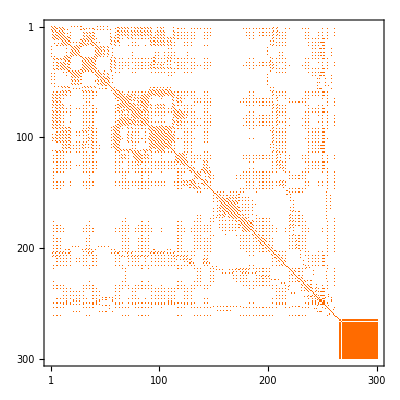

```mathematica
MatrixPlot[rm]
```